```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

## Ze plot data

#### Orbit 3368

```mathematica
time={"21:06:35.072","21:06:35.704","21:06:36.335","21:06:36.967","21:06:37.598","21:06:38.230","21:06:38.862","21:06:39.493","21:06:40.125","21:06:40.756","21:06:41.388","21:06:42.019","21:06:42.651","21:06:43.282","21:06:43.914","21:06:44.546","21:06:45.177","21:06:45.809","21:06:46.440","21:06:47.072","21:06:47.703","21:06:48.335","21:06:48.966","21:06:49.598","21:06:50.230","21:06:50.861","21:06:51.493","21:06:52.124","21:06:52.756","21:06:53.387","21:06:54.019","21:06:54.650","21:06:55.282","21:06:55.914","21:06:56.545","21:06:57.177","21:06:57.808","21:06:58.440","21:06:59.071","21:06:59.703","21:07:00.334","21:07:00.966","21:07:01.598","21:07:02.229","21:07:02.861","21:07:03.492","21:07:04.124","21:07:04.755","21:07:05.387","21:07:06.018","21:07:06.650","21:07:07.282","21:07:07.913","21:07:08.545","21:07:09.176","21:07:09.808","21:07:10.439","21:07:11.071","21:07:11.702","21:07:12.334","21:07:12.966","21:07:13.597","21:07:14.229","21:07:14.860","21:07:15.492","21:07:16.123","21:07:16.755","21:07:17.386","21:07:18.018","21:07:18.650","21:07:19.281","21:07:19.913","21:07:20.544","21:07:21.176","21:07:21.807","21:07:22.439","21:07:23.070","21:07:23.702","21:07:24.334","21:07:24.965","21:07:25.597","21:07:26.228","21:07:26.860","21:07:27.491","21:07:28.123","21:07:28.754","21:07:29.386","21:07:30.018","21:07:30.649","21:07:31.281","21:07:31.912","21:07:32.544","21:07:33.175","21:07:33.807","21:07:34.438","21:07:35.070","21:07:35.701","21:07:36.333","21:07:36.965","21:07:37.596","21:07:38.228","21:07:38.859","21:07:39.491","21:07:40.122","21:07:40.754","21:07:41.385","21:07:42.017","21:07:42.649","21:07:43.280","21:07:43.912","21:07:44.543","21:07:45.175","21:07:45.806","21:07:46.438","21:07:47.069","21:07:47.701","21:07:48.333","21:07:48.964","21:07:49.596","21:07:50.227","21:07:50.859","21:07:51.490","21:07:52.122","21:07:52.753","21:07:53.385","21:07:54.017","21:07:54.648","21:07:55.280","21:07:55.911","21:07:56.543","21:07:57.174","21:07:57.806","21:07:58.437","21:07:59.069","21:07:59.701","21:08:00.332","21:08:00.964","21:08:01.595","21:08:02.227","21:08:02.858","21:08:03.490","21:08:04.121","21:08:04.753","21:08:05.385","21:08:06.016","21:08:06.648","21:08:07.279","21:08:07.911","21:08:08.542","21:08:09.174","21:08:09.805","21:08:10.437","21:08:11.068","21:08:11.700","21:08:12.332","21:08:12.963","21:08:13.595","21:08:14.226","21:08:14.858","21:08:15.489","21:08:16.121","21:08:16.752","21:08:17.384","21:08:18.016","21:08:18.647","21:08:19.279","21:08:19.910","21:08:20.542","21:08:21.173","21:08:21.805","21:08:22.436","21:08:23.068","21:08:23.700","21:08:24.331","21:08:24.963","21:08:25.594","21:08:26.226","21:08:26.857","21:08:27.489","21:08:28.120","21:08:28.752","21:08:29.383","21:08:30.015","21:08:30.647","21:08:31.278","21:08:31.910","21:08:32.541","21:08:33.173","21:08:33.804","21:08:34.436","21:08:35.067","21:08:35.699","21:08:36.331","21:08:36.962","21:08:37.594","21:08:38.225","21:08:38.857","21:08:39.488","21:08:40.120","21:08:40.751","21:08:41.383","21:08:42.015","21:08:42.646","21:08:43.278","21:08:43.909"};
pots={815.36,470.40,407.68,344.96,689.92,470.40,470.40,470.40,564.48,407.68,344.96,344.96,344.96,344.96,564.48,344.96,344.96,815.36,1881.60,407.68,1630.72,1379.84,1128.96,940.80,940.80,815.36,815.36,344.96,815.36,940.80,940.80,2257.92,2257.92,1881.60,1379.84,689.92,689.92,815.36,815.36,689.92,470.40,470.40,344.96,407.68,470.40,470.40,564.48,689.92,815.36,689.92,815.36,815.36,689.92,815.36,815.36,815.36,815.36,689.92,815.36,815.36,815.36,815.36,689.92,564.48,564.48,564.48,689.92,815.36,940.80,940.80,815.36,940.80,940.80,815.36,815.36,689.92,564.48,564.48,564.48,564.48,407.68,470.40,470.40,564.48,564.48,564.48,689.92,689.92,815.36,815.36,689.92,689.92,689.92,689.92,689.92,815.36,689.92,689.92,564.48,689.92,689.92,689.92,564.48,564.48,470.40,470.40,470.40,470.40,564.48,689.92,689.92,564.48,564.48,470.40,407.68,407.68,407.68,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,470.40,689.92,815.36,940.80,1128.96,1379.84,1630.72,2257.92,2759.68,2759.68,2759.68,2759.68,2759.68,2759.68,3261.44,3261.44,3261.44,3261.44,3261.44,3261.44,3261.44,3763.20,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,5519.36,5519.36,5519.36,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,3763.20,3261.44,3261.44,3261.44,2759.68,2759.68,2257.92,2257.92,1630.72,1630.72,1379.84,1379.84,1379.84,1128.96,940.80,940.80,815.36,689.92,564.48,564.48,470.40,564.48,564.48,470.40,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96};
curs={0.008,0.011,0.009,0.010,0.014,0.011,0.010,0.011,0.015,0.074,0.140,0.069,0.190,0.247,0.052,0.219,1.248,1.663,1.236,1.423,0.761,0.509,0.259,0.209,0.199,0.173,0.161,0.202,0.139,0.187,0.143,0.585,3.956,3.570,1.784,0.943,0.875,1.206,1.046,0.712,0.588,0.465,0.498,0.479,0.529,0.421,0.438,0.529,0.571,0.440,0.604,0.586,0.444,0.822,0.670,0.613,0.578,0.479,0.354,0.409,0.427,0.396,0.359,0.315,0.270,0.266,0.421,0.577,0.892,0.959,0.894,1.056,1.016,0.946,0.813,0.440,0.317,0.344,0.287,0.259,0.201,0.236,0.279,0.410,0.386,0.307,0.305,0.360,0.439,0.436,0.378,0.357,0.368,0.365,0.420,0.431,0.410,0.405,0.311,0.355,0.287,0.474,0.459,0.465,0.413,0.348,0.379,0.521,0.380,0.762,0.784,0.700,0.626,0.536,0.395,0.429,0.426,0.283,0.138,0.056,0.044,0.064,0.098,0.090,0.077,0.110,0.306,0.532,0.645,0.704,0.886,0.933,0.693,0.937,0.946,0.998,1.139,1.134,1.185,1.072,1.169,1.328,1.501,1.482,1.556,1.692,1.914,1.994,1.994,1.452,1.499,1.565,1.770,2.063,2.243,2.385,2.629,2.504,2.274,1.971,1.952,1.864,1.658,1.547,1.518,1.390,1.241,1.086,0.970,0.835,0.750,0.733,0.661,0.504,0.457,0.435,0.454,0.437,0.421,0.430,0.400,0.366,0.346,0.331,0.299,0.303,0.278,0.215,0.251,0.234,0.235,0.277,0.314,0.334,0.312,0.224,0.196,0.177,0.229,0.155,0.120,0.191,0.172,0.206,0.262};
curErrs={0.013,0.005,0.006,0.006,0.003,0.035,0.009,0.003,0.015,0.016,0.021,0.230,0.025,0.020,0.358,0.011,0.033,0.042,0.077,0.053,0.071,0.060,0.060,0.048,0.198,0.843,0.022,0.014,0.013,0.021,0.013,0.023,0.081,0.071,0.051,0.045,0.046,0.046,0.042,0.032,0.026,0.027,0.020,0.031,0.032,0.028,0.030,0.035,0.034,0.023,0.033,0.041,0.039,0.046,0.044,0.038,0.035,0.029,0.025,0.034,0.038,0.032,0.031,0.032,0.025,0.022,0.031,0.051,0.066,0.059,0.057,0.064,0.067,0.066,0.052,0.063,0.037,0.055,0.035,0.029,0.042,0.034,0.028,0.025,0.023,0.020,0.019,0.019,0.020,0.021,0.019,0.024,0.026,0.020,0.023,0.021,0.022,0.020,0.020,0.026,0.020,0.026,0.027,0.023,0.024,0.021,0.022,0.029,0.026,0.037,0.042,0.032,0.034,0.031,0.023,0.030,0.033,0.027,0.020,0.013,0.009,0.015,0.024,0.017,0.029,0.030,0.023,0.029,0.033,0.033,0.037,0.066,0.051,0.054,0.053,0.053,0.055,0.054,0.053,0.061,0.064,0.083,0.077,0.077,0.079,0.079,0.075,0.114,0.105,0.121,0.091,0.091,0.102,0.100,0.104,0.143,0.160,0.175,0.152,0.122,0.139,0.107,0.113,0.131,0.126,0.142,0.126,0.103,0.114,0.089,0.079,0.093,0.093,0.107,0.076,0.091,0.150,0.093,0.070,0.076,0.090,0.063,0.089,0.085,0.061,0.062,0.041,0.038,0.030,0.037,0.037,0.053,0.070,0.047,0.071,0.024,0.021,0.019,0.020,0.020,0.022,0.020,0.029,0.036,0.038};
jes={0.017,0.018,0.010,0.010,0.013,0.013,0.020,0.031,0.015,0.039,0.074,0.047,0.078,0.090,0.044,0.133,0.734,1.312,1.703,1.464,0.904,0.573,0.276,0.206,0.170,0.133,0.113,0.126,0.116,0.167,0.152,0.911,8.154,5.904,2.050,0.707,0.624,0.961,0.812,0.463,0.345,0.251,0.231,0.254,0.313,0.252,0.277,0.374,0.445,0.317,0.467,0.467,0.344,0.678,0.546,0.487,0.469,0.377,0.296,0.340,0.365,0.316,0.278,0.233,0.170,0.169,0.307,0.435,0.764,0.801,0.733,0.888,0.893,0.777,0.647,0.295,0.207,0.234,0.192,0.184,0.123,0.143,0.181,0.282,0.273,0.235,0.241,0.307,0.403,0.393,0.315,0.282,0.286,0.275,0.340,0.350,0.331,0.313,0.225,0.262,0.224,0.341,0.302,0.278,0.218,0.191,0.198,0.281,0.220,0.484,0.508,0.442,0.368,0.289,0.197,0.201,0.199,0.115,0.056,0.029,0.019,0.027,0.054,0.035,0.030,0.048,0.133,0.300,0.436,0.556,0.835,1.007,0.864,1.364,1.830,2.239,2.626,2.670,2.838,2.538,2.898,3.501,4.110,4.092,4.318,4.755,5.586,5.961,6.268,4.804,5.262,5.585,6.515,7.726,8.331,8.963,9.993,9.717,9.298,8.238,8.125,7.818,6.772,6.230,5.960,5.704,5.209,4.425,3.803,3.156,2.724,2.587,2.315,1.592,1.411,1.315,1.405,1.256,1.137,1.044,0.931,0.847,0.741,0.683,0.586,0.545,0.462,0.321,0.371,0.368,0.334,0.362,0.410,0.510,0.475,0.336,0.256,0.240,0.285,0.249,0.214,0.254,0.230,0.240,0.236};
jeErrs={0.014,0.096,0.019,0.021,0.056,0.085,0.011,0.020,0.041,0.154,0.057,0.589,0.043,0.172,0.097,0.154,0.082,0.110,0.506,0.510,0.261,0.206,0.165,0.439,0.173,1.219,0.146,0.134,0.080,0.062,0.057,0.089,0.440,0.326,0.203,0.214,0.129,0.142,0.132,0.087,0.102,0.075,0.160,0.073,0.079,0.084,0.143,0.096,0.100,0.078,0.097,0.122,0.104,0.142,0.181,0.117,0.118,0.101,0.078,0.120,0.127,0.105,0.116,0.102,0.064,0.078,0.098,0.196,0.207,0.208,0.290,0.222,0.206,0.224,0.158,0.177,0.093,0.136,0.101,0.082,0.144,0.081,0.104,0.094,0.071,0.072,0.071,0.069,0.077,0.081,0.077,0.089,0.100,0.066,0.077,0.067,0.082,0.070,0.088,0.092,0.090,0.074,0.091,0.096,0.055,0.063,0.111,0.083,0.085,0.099,0.118,0.088,0.102,0.071,0.172,0.102,0.089,0.049,0.050,0.034,0.017,0.027,0.154,0.030,0.076,0.050,0.045,0.193,0.092,0.099,0.142,0.270,0.188,0.239,0.288,0.313,0.296,0.310,0.382,0.372,0.409,0.546,0.540,0.523,0.536,0.520,0.624,0.891,0.747,0.948,0.688,0.699,0.891,0.872,0.959,1.324,1.500,1.448,1.319,1.082,1.242,1.016,1.169,1.192,1.038,1.168,1.028,0.860,0.906,0.799,1.400,0.830,0.815,0.635,0.437,1.868,6.722,1.327,8.343,0.636,0.500,0.299,0.548,0.389,0.373,0.311,0.203,0.374,0.127,0.158,0.187,0.161,0.889,0.140,0.176,0.123,0.070,0.076,0.076,0.067,0.077,0.088,0.057,0.231,0.076};
```

### Lil plot to check out J-V relation on the fly

```mathematica
ind1Start=0;ind1End=130;ind1Init=78;ind2Init=131;(*Good J-V, but Maxwellian!*)
```

```mathematica
ind1Start=0;ind1End=40;ind1Init=33;ind2Init=46; (*Maybe kappa?*)
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{200,Max[pots]},{0,Max[curs]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Lil plot to check out energy flux–voltage relation on the fly

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]},{0,Max[jes]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

J-V fits

## Nonlinear fits for current density

### Fit data

```mathematica
inds1=Range[33,46];
inds2=Range[78,131];
inds3=inds1~Join~inds2;
```

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

### Now the fits

```mathematica
kConstraints={0.01<kFitN<10,1<kFitT<4000,3<kFitRB<100,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,1<gFitT<4000,3<gFitRB<100};
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[plotData1,{kModel,kConstraints},{{kFitN,2},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->plotDataWts1]
```

FittedModel[10.1477 (1-0.99/((1+6.86663×10^-6 pot)^19.))]

```mathematica
gFit=NonlinearModelFit[plotData1,{gModel,gConstraints},{{gFitN,2},{gFitT,300},{gFitRB,10}},pot,Weights->plotDataWts1]
```

FittedModel[9.95261 (1-0.99 ⅇ^(-0.000133144 pot))]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*plotDataWts1]/kDOF}
```

{0.429129,79.5153,100.,20.,91.1598}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*plotDataWts1]/gDOF}
```

{0.427982,75.8653,100.,81.9654}

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.429129 | 16.5686 | 0.0259002 | 0.979847
kFitT | 79.5153 | 10928.2 | 0.00727615 | 0.994338
kFitRB | 100. | 24114.2 | 0.00414694 | 0.996773
kFitKappa | 20. | 103747. | 0.000192776 | 0.99985

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.427982 | 0.70467 | 0.607351 | 0.555948
gFitT | 75.8653 | 368.941 | 0.20563 | 0.840836
gFitRB | 100. | 228.011 | 0.438575 | 0.669459

### Ze plot

```mathematica
plotData1[[;;,1]]
```

{2257.92,1881.6,1379.84,689.92,689.92,815.36,815.36,689.92,470.4,470.4,344.96,407.68,470.4,470.4}

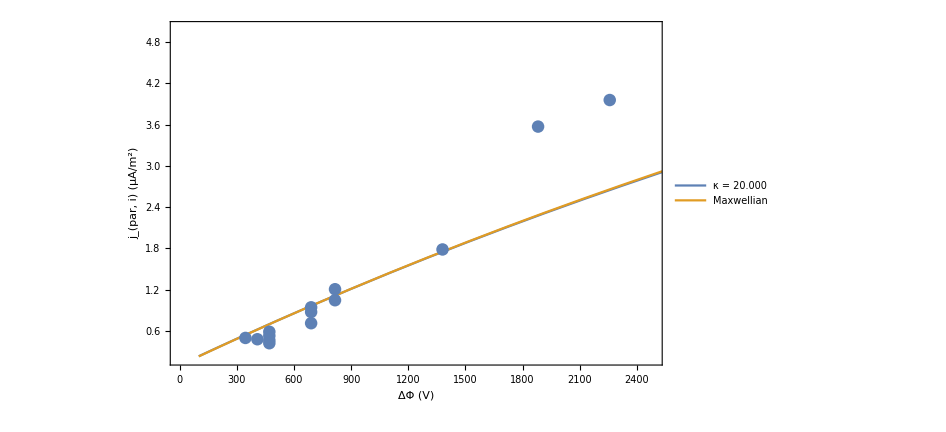

```mathematica
Show[Plot[{kFit[pot],gFit[pot]},{pot,100,10000},PlotRange->{{0,Max[plotData1[[;;,1]]]*11/10},{0.2,5}},PlotLegends->((Style[#,20])&/@{StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]]
```

## Nonlinear fits for energy flux

### Ze Fits

```mathematica
kConstraints={0.01<kFitN<10,80<kFitT<4000,3<kFitRB<100,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,80<gFitT<4000,3<gFitRB<100};
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFitJeV=NonlinearModelFit[jeData1,{kModelJeV,kConstraints},{{kFitN,2},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->jeDataWts1]
```

FittedModel[0.856315 (2-1.04211/((1+6.82508×10^-6 pot)^17.9998)-(1.00053 («1»))/(1+«22» pot)^(«19»)+0.0121622 pot)]

```mathematica
gFitJeV=NonlinearModelFit[jeData1,{gModelJeV,gConstraints},{{gFitN,2},{gFitT,300},{gFitRB,10}},pot,Weights->jeDataWts1]
```

FittedModel[0.842021 (2-ⅇ^(-0.000126263 pot) (1.98+0.0125 pot)+0.0125 pot)]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeDataWts1]/kDOF}
```

{0.437323,80.0001,100.,19.9998,6.50628}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeDataWts1]/gDOF}
```

{0.438992,80.,100.,6.04861}

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.437323 | 21.6507 | 0.020199 | 0.984282
kFitT | 80.0001 | 7229.01 | 0.0110665 | 0.991388
kFitRB | 100. | 23746.5 | 0.00421115 | 0.996723
kFitKappa | 19.9998 | 97939.6 | 0.000204205 | 0.999841

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.438992 | 0.208302 | 2.10747 | 0.0588338
gFitT | 80. | 194.379 | 0.411567 | 0.688562
gFitRB | 100. | 335.281 | 0.298257 | 0.771065

### Ze plot

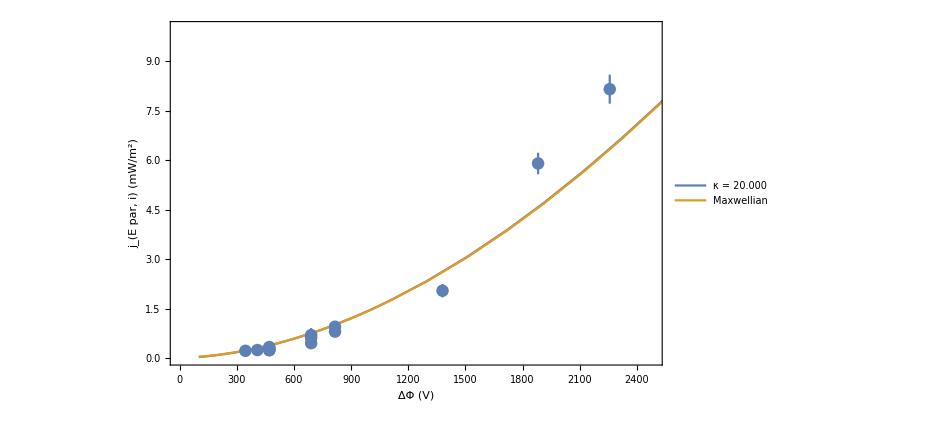

```mathematica
Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,100,10000},PlotRange->{{0,Max[jeData1[[;;,1]]]*11/10},{0,10}},PlotLegends->((Style[#,20])&/@{StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(E par, i) (mW/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorJe1]]
```

## Simultaneously fit both sets of data, allowing RB to be different for each

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDat = Join[plotData1/.{x_,y_}->{1,x,y},plotData2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=plotDataWts1~Join~plotDataWts2;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gCombFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kCombConstraints={1<kFitRB1<5000,1<kFitRB2<5000,50<kFitT<5000,0.1<kFitN<10,1.51<kFitKappa<35};
gCombConstraints={1<gFitRB1<5000,1<gFitRB2<5000,50<gFitT<5000,0.1<gFitN<10};
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB1,3},{kFitRB2,10},{kFitT,300},{kFitN,1},{kFitKappa,5}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,(0.0266987 «5»)/((1-1/(«19»)) «1» Gamma[«1»]),set==2,(0.0266987 0.178864 «19» √(«1») (1-(1-1/107.164) (1+«1»)^(1-«19»)) Gamma[1+1.51])/((1-1/1.51) 1.51^(3/2) Gamma[-1/2+1.51])]]

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gCombConstraints},{{gFitRB1,3},{gFitRB2,10},{gFitT,300},{gFitN,1}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,0.0266987 0.364857 (1-ⅇ^(-pot/(«1»)) (1-1/(«18»))) 5000. √50.,set==2,0.0266987 0.364857 (1-ⅇ^(-pot/((-1+19.1135) «18»)) (1-1/19.1135)) 19.1135 √50.]]

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB1,kCombRB2,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF}
```

{5000.,107.164,840.445,0.178864,1.51,57.0021}

```mathematica
{gCombRB1,gCombRB2,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF}
```

{5000.,19.1135,50.,0.364857,64.0348}

```mathematica
RBinit1=gCombRB1;RBinit2=gCombRB2;Tminit=gCombT;nminit=gCombN;
```

### Mess ‘round

```mathematica
Manipulate[Row[{Manipulate[Show[Plot[{JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa1,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]],{{RB1,RBinit1},1.01,5000},{{kappa1,kappainit},1.501,35}],Manipulate[Show[Plot[{JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa2]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa2,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData2]],{{RB2,RBinit2},1.01,5000},{{kappa2,kappainit},1.501,35}]}],{{Tm,Tminit},3,500},{{nm,nminit},0.1,5}]
```

### Just tell ‘em, Hammer

```mathematica
combRepl={RB1->gCombRB1,RB2->gCombRB2,Tm->gCombT,nm->gCombN,kappa1->kCombKappa};
```

```mathematica
parNames={"T_m : ","n_m : ","R_B : "};
vals1=MapThread[NumberForm,{({Tm,nm,RB1}/.combRepl),{{3,0},{3,2},{3,1}}}];
vals2=MapThread[NumberForm,{({Tm,nm,RB2}/.combRepl),{{3,0},{3,2},{3,1}}}];
```

```mathematica
parTable1=Text[Grid[Transpose[{parNames,vals1}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
parTable2=Text[Grid[Transpose[{parNames,vals2}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
```

```mathematica
title1=StringJoin@Riffle[StringDrop[time[[inds1[[{1,-1}]]]],11],"–"]
title2=StringJoin@Riffle[StringDrop[time[[inds2[[{1,-1}]]]],11],"–"]
```

09:26:11.332–09:26:22.708

09:26:56.837–09:27:06.950

```mathematica
seg1Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{0.5,2.5}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 1 (`1`)",title1],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable1,Scaled[{0.1,0.8}]]];
```

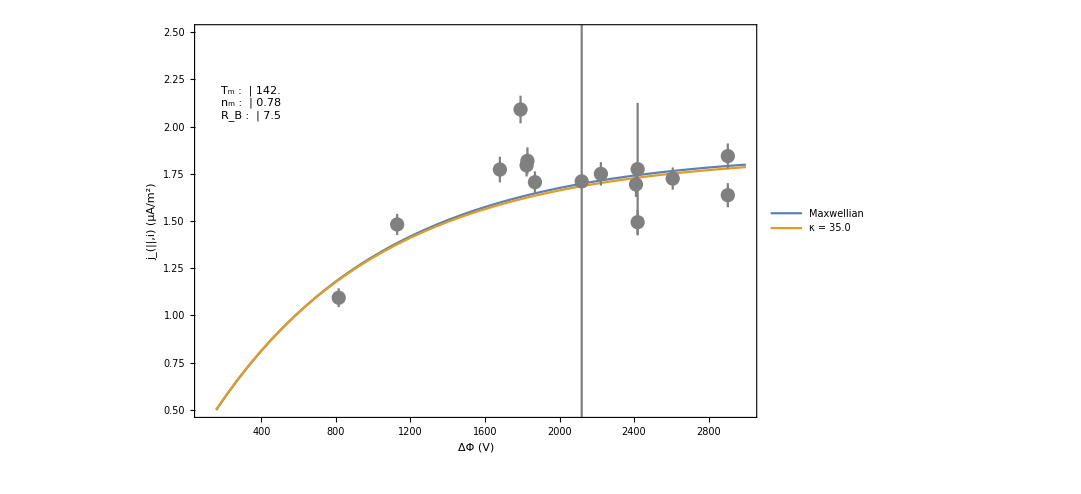

```mathematica
seg1Plot=Show[seg1Plotp1,ErrorListPlot[errorData1,PlotStyle->Gray]]
```

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

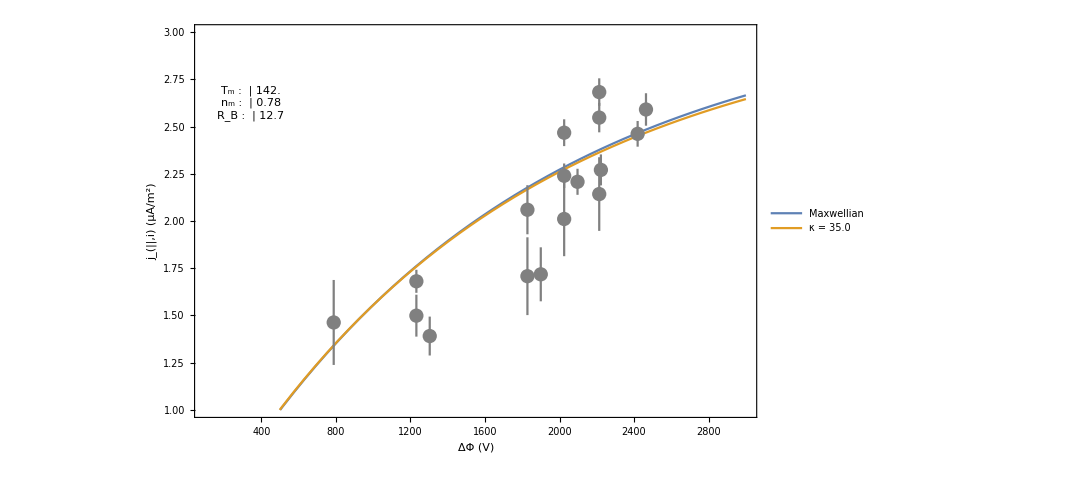

```mathematica
seg2Plot=Show[seg2Plotp1,ErrorListPlot[errorData2,PlotStyle->Gray]]
```

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

J_E-V fits

## Nonlinear fits for first portion of arc

### Now the actual fits

```mathematica
kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<100000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<100000};
```

```mathematica
kModel = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jeData1,{kModel,kConstraints},{{kFitN,1},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->jeDataWts1]
```

FittedModel[190.129 (1-0.999/((1+7.8012×10^-6 pot)^1.78314))]

```mathematica
gFit=NonlinearModelFit[jeData1,{gModel,gConstraints},{{gFitN,1},{gFitT,300},{gFitRB,10}},pot,Weights->jeDataWts1]
```

FittedModel[257.069 (1-0.999 ⅇ^(-0.00001001 pot))]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*plotDataWts1]/kDOF}
```

{0.783318,100.,1000.,2.78314,1033.21}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*plotDataWts1]/gDOF}
```

{0.962852,100.,1000.,1005.44}

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.783318 | 1369.41 | 0.000572012 | 0.999548
kFitT | 100. | 993091. | 0.000100696 | 0.99992
kFitRB | 1000. | 8.97918×10^6 | 0.000111369 | 0.999912
kFitKappa | 2.78314 | 45635.4 | 0.0000609864 | 0.999952

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.962852 | 4.0853 | 0.235687 | 0.815277
gFitT | 100. | 1090.19 | 0.0917273 | 0.927524
gFitRB | 1000. | 56450.7 | 0.0177146 | 0.985984

### Ze plot

```mathematica
plotData1[[;;,1]]
```

{1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,940.8,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1128.96,940.8,1128.96,1128.96,1128.96,940.8,940.8,1128.96,1881.6,2257.92,1881.6,2257.92,2257.92,2257.92,2257.92,2759.68,2759.68,2759.68,3261.44}

```mathematica
Show[Plot[{kFit[pot],gFit[pot]},{pot,100,10000},PlotRange->{{0,Max[plotData1[[;;,1]]]*11/10},{0.2,5}},PlotLegends->((Style[#,20])&/@{StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]]
```

```mathematica
t
```

## Nonlinear fits for second portion of arc

### Now the actual fits

```mathematica
kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[plotData2,{kModel,kConstraints},{{kFitN,1},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->plotDataWts2]
```

FittedModel[32.9544 (1-0.999/(1+0.0000189996 pot)^1.02685)]

```mathematica
gFit=NonlinearModelFit[plotData2,{gModel,gConstraints},{{gFitN,1},{gFitT,300},{gFitRB,10}},pot,Weights->plotDataWts2]
```

FittedModel[60.7716 (1-0.999 ⅇ^(-0.00001001 pot))]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*plotDataWts2]/kDOF}
```

{0.153169,100.,999.999,2.02685,64.0413}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*plotDataWts2]/gDOF}
```

{0.227621,100.,999.998,62.6737}

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.153169 | 55.8589 | 0.00274208 | 0.997823
kFitT | 100. | 308806. | 0.000323828 | 0.999743
kFitRB | 999.999 | 1.56973×10^6 | 0.00063705 | 0.999494
kFitKappa | 2.02685 | 3348.16 | 0.000605363 | 0.999519

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {gFitN, 0.22762063587153794, 0.15972885755558222, 1.4250439110060675, 0.16000705892709144}, {gFitT, 100.00001798377369, 204.31773587826078, 0.4894338592483082, 0.6265541771816758}, {gFitRB, 999.9978745279175, 26382.65996011885, 0.037903603201479945, 0.9699069518816414}}
```

### Ze plot

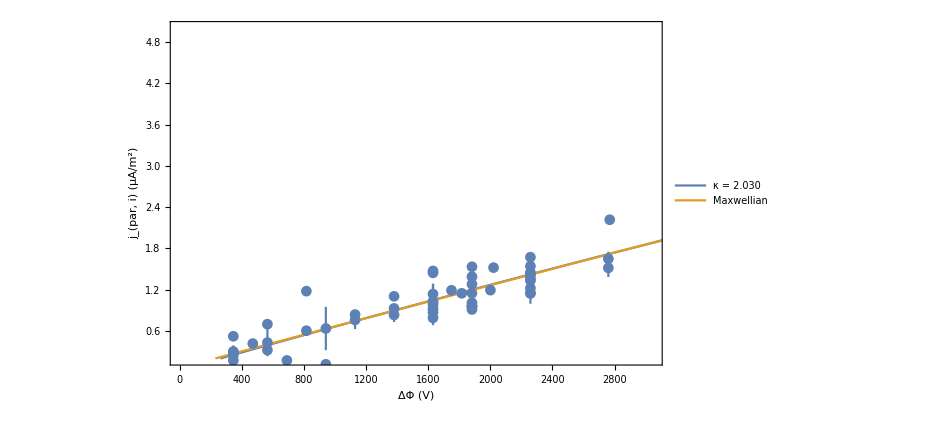

```mathematica
Show[Plot[{kFit[pot],gFit[pot]},{pot,100,10000},PlotRange->{{0,Max[plotData2[[;;,1]]]*11/10},{0.2,5}},PlotLegends->((Style[#,20])&/@{StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorData2]]
```

## Linear model for second half of arc

```mathematica
lm=LinearModelFit[plotData2,x,x,Weights->plotDataWts2]
```

FittedModel[0.571783+0.000828171 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.571783 | 0.209522 | 2.72899 | 0.0155285
x | 0.000828171 | 0.000104376 | 7.93453 | 9.52667×10^-7

```mathematica
Kmeas=(lm["BestFitParameters"])[[2]]
```

0.000828171

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.571783 | 0.209522 | {0.125197,1.01837}
x | 0.000828171 | 0.000104376 | {0.000605699,0.00105064}

```mathematica
lm["AdjustedRSquared"]
```

0.794758

#### See it

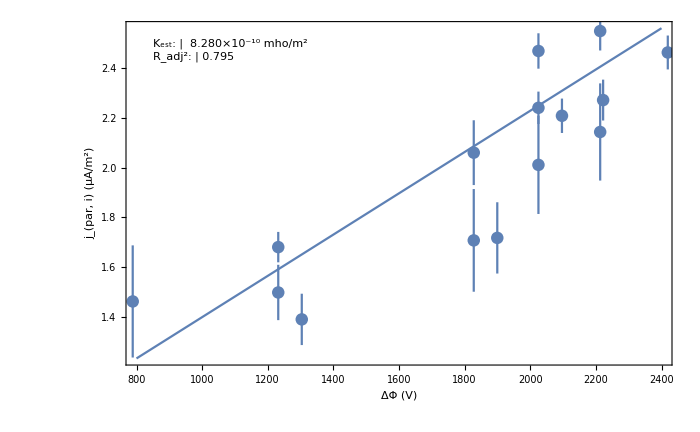

```mathematica
Show[Plot[lm[x],{x,800,2400},Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18),Epilog->Inset[TextGrid[Map[(Style[#,18])&,{{StringForm["K_est:"],StringForm[" `1` mho/m^2",NumberForm[Kmeas*1*^-6,{3,3},ScientificNotationThreshold->{-2,2}]]},{StringForm["R_adj^2:"],NumberForm[lm["AdjustedRSquared"],{3,3}]}},{2}]],Scaled[{0.05,0.95}],{-1,1}]],ErrorListPlot[errorData2]]
```

### Assess it

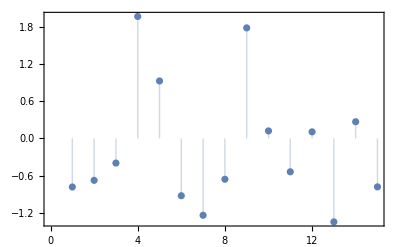

```mathematica
ListPlot[lm["StandardizedResiduals"],Frame->True,Filling->Axis]
```

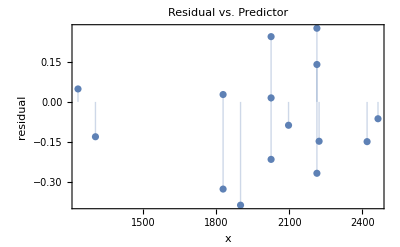

```mathematica
ListPlot[Transpose[{pots[[inds2]],lm["FitResiduals"]}],Frame->True,Filling->0,FrameLabel->{"x","residual"},PlotLabel->"Residual vs. Predictor"]
```

## Artificially combine parts of each

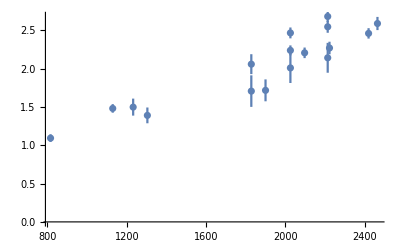

```mathematica
ErrorListPlot[errorData3]
```

## Simultaneously fit both sets of data, allowing RB to be different for each

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDat = Join[plotData1/.{x_,y_}->{1,x,y},plotData2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=plotDataWts1~Join~plotDataWts2;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gCombFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kCombConstraints={1<kFitRB1<5000,1<kFitRB2<5000,50<kFitT<5000,0.1<kFitN<10,1.51<kFitKappa<35};
gCombConstraints={1<gFitRB1<5000,1<gFitRB2<5000,50<gFitT<5000,0.1<gFitN<10};
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB1,3},{kFitRB2,10},{kFitT,300},{kFitN,1},{kFitKappa,5}},{set,pot},Weights->combWts]
```

$Aborted

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gCombConstraints},{{gFitRB1,3},{gFitRB2,10},{gFitT,300},{gFitN,1}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,0.0266987 0.364857 (1-ⅇ^(-pot/(«1»)) (1-1/(«18»))) 5000. √50.,set==2,0.0266987 0.364857 (1-ⅇ^(-pot/((-1+19.1135) «18»)) (1-1/19.1135)) 19.1135 √50.]]

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB1,kCombRB2,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF}
```

{5000.,107.164,840.445,0.178864,1.51,57.0021}

```mathematica
{gCombRB1,gCombRB2,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF}
```

{5000.,19.1135,50.,0.364857,64.0348}

```mathematica
RBinit1=gCombRB1;RBinit2=gCombRB2;Tminit=gCombT;nminit=gCombN;
```

```mathematica
RBinit1=kCombRB1;RBinit2=kCombRB2;Tminit=kCombT;nminit=kCombN;kappainit=kCombN;
```

### Mess ‘round

```mathematica
Manipulate[Row[{Manipulate[Show[Plot[{JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa1,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]],{{RB1,RBinit1},1.01,5000},{{kappa1,kappainit},1.501,35}],Manipulate[Show[Plot[{JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa2]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa2,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData2]],{{RB2,RBinit2},1.01,5000},{{kappa2,kappainit},1.501,35}]}],{{Tm,Tminit},3,500},{{nm,nminit},0.1,5}]
```

### Just tell ‘em, Hammer

```mathematica
combRepl={RB1->gCombRB1,RB2->gCombRB2,Tm->gCombT,nm->gCombN,kappa1->kCombKappa};
```

```mathematica
parNames={"T_m : ","n_m : ","R_B : "};
vals1=MapThread[NumberForm,{({Tm,nm,RB1}/.combRepl),{{3,0},{3,2},{3,1}}}];
vals2=MapThread[NumberForm,{({Tm,nm,RB2}/.combRepl),{{3,0},{3,2},{3,1}}}];
```

```mathematica
parTable1=Text[Grid[Transpose[{parNames,vals1}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
parTable2=Text[Grid[Transpose[{parNames,vals2}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
```

```mathematica
title1=StringJoin@Riffle[StringDrop[time[[inds1[[{1,-1}]]]],11],"–"]
title2=StringJoin@Riffle[StringDrop[time[[inds2[[{1,-1}]]]],11],"–"]
```

09:26:11.332–09:26:22.708

09:26:56.837–09:27:06.950

```mathematica
seg1Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{0.5,2.5}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 1 (`1`)",title1],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable1,Scaled[{0.1,0.8}]]];
```

```mathematica
seg1Plot=Show[seg1Plotp1,ErrorListPlot[errorData1,PlotStyle->Gray]]
```

-Graphics-

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

```mathematica
seg2Plot=Show[seg2Plotp1,ErrorListPlot[errorData2,PlotStyle->Gray]]
```

-Graphics-

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

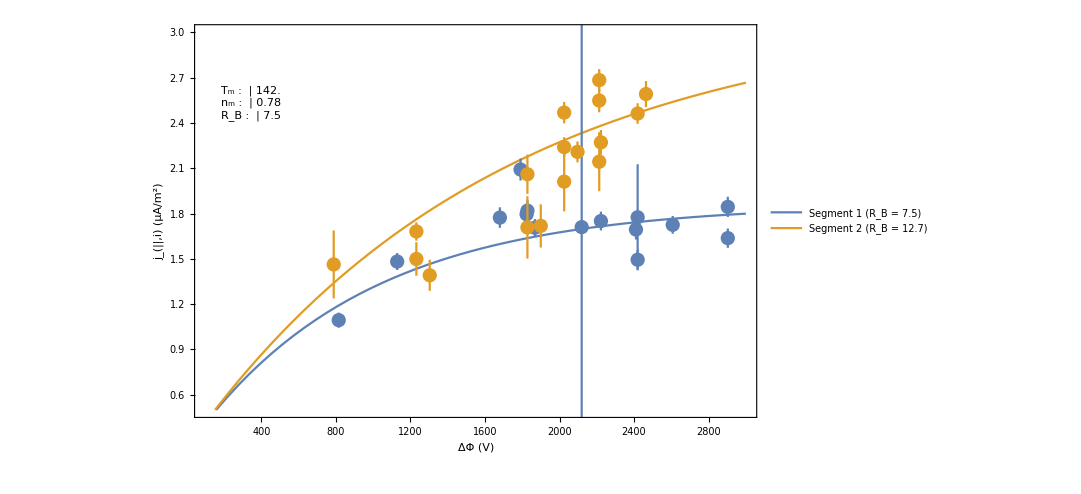

```mathematica
seg2Plot=Show[Plot[Evaluate@(({JVMaxwellian[pot,RB1,Tm,nm],JVMaxwellian[pot,RB2,Tm,nm]})/.combRepl),{pot,100,3000},PlotRange->{Full,{0.5,3}},PlotLegends->Map[(Style[#,23])&,MapThread[(StringForm["Segment `1` (R_B = `2`)",#1,NumberForm[#2,{3,1}]])&,({{"1","2"},{RB1,RB2}}/.combRepl)]],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style["Combined Segments",Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable1,Scaled[{0.1,0.8}]]],ErrorListPlot[{errorData1,errorData2}]]
```

```mathematica
t
```